```mathematica
Clear["Global`*"]
```

```mathematica
M:=0.0005167834223142191
p:=4
μ:=1.0
ϕini:=0.0455142
ϕend:=0.659399
V[p_,t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[p_,t_]=D[V[p,t],ϕ[t]];
sol=NDSolve[{3 a'[t]/a[t] ϕ'[t]+Vp[p,t]==0,
a'[t]==a[t]Sqrt[1/3 V[p,t]],ϕ[0]==ϕini,a[0]==1},{ϕ,a},{t,- 3.11 10^9,2.07 10^12}];
asr[t_]:=(a/.First[sol])[t]
asrp[t_]=D[asr[t],{t,1}];
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
ϕsrpp[t_]=D[ϕsr[t],{t,2}];
ϕsrppp[t_]=D[ϕsr[t],{t,3}];
Vt[p_,t_]:= M^4 (1-(ϕsr[t]/μ)^p)
Hsr[p_,t_]:=1/Sqrt[3]Sqrt[Vt[p,t]]
Hsrp[p_,t_]=D[Hsr[p,t],{t,1}];
Vphi[p_,ϕ_]:=M^4 (1-(ϕ/μ)^p)
Vp[p_,ϕ_]=D[V[p,ϕ],{ϕ,1}];
Vpp[p_,ϕ_]=D[V[p,ϕ],{ϕ,2}];
(*Parameters*)
ϵH1[p_,t_]:=-Hsrp[p,t]/Hsr[p,t]^2
ϵH2[p_,t_]=1/Hsr[p,t] D[ϵH1[p,t],{t,1}];
δH1[p_,t_]:=ϕsrpp[t]/(Hsr[p,t] ϕsrp[t])
δH2[p_,t_]:=ϕsrppp[t]/(Hsr[p,t]^2 ϕsrp[t])
α:=0.729637
(*First order*)
PSsr1[t_]:= (1+(4 α-2) ϵH1[p,t]+2 α δH1[p,t]) (Hsr[p,t]^2/(2 π ϕsrp[t]))^2
nSsr1[t_]:=1-4 ϵH1[p,t]-2 δH1[p,t]
PTsr1[t_]:=(1+(2 α-2) ϵH1[p,t])(Hsr[p,t]/(2 π))^2
nTsr1[t_]:=-2 ϵH1[p,t]
(*Second order*)
PSsr2[t_]:=(1+(4 α-2) ϵH1[p,t]+2 α δH1[p,t]+(4 α^2-23+7 π^2/3) ϵH1[p,t]^2+(3 α^2+2α-22+29 π^2/12) ϵH1[p,t] δH1[p,t]+(3 α^2-4+5 π^2/12) δH1[p,t]^2 + (-α^2+π^2/12) δH2[p,t]) (Hsr[p,t]^2/(2 π ϕsrp[t]))^2
nSsr2[t_]:=1-4 ϵH1[p,t]-2 δH1[p,t]+(8 α-8)ϵH1[p,t]^2+(10 α-6) ϵH1[p,t] δH1[p,t]-2 α δH1[p,t]^2+2 α δH2[p,t]
PTsr2[t_]:=(1+(2 α-2) ϵH1[p,t]+(2 α^2-2 α-3+π^2/2) ϵH1[p,t]^2+(-α^2+2 α-2+π^2/12)ϵH2[p,t])(Hsr[p,t]/(2 π))^2
nTsr2[t_]:=-2 ϵH1[p,t]-2 ϵH1[p,t]^2+(2 α-2) ϵH2[p,t]
teval[k_]:=(t/.First[FindRoot[k==asr[t] (Hsr[p,t]),{t,150,100}]])
(*Ration*)
rsr[t_]:=16 ϵH1[p,t] (1+CC ϵH2[p,t])
CC:=-0.7296 
kcomoving[kphy_]:=kphy*100*(2.99792458*^5)/(Sqrt[8Pi]67.4)
```

General::munfl: 1/(4.99962×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(5.86528×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(6.88083×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
ϕsr[teval[0.05]]
```

0.051217+0. ⅈ

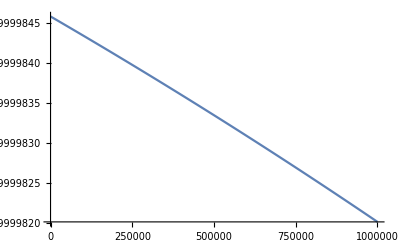

```mathematica
Plot[0.05-asr[t] Hsr[p,t],{t,0,10^6}]
```

```mathematica
teval[0.05]
```

8.2297×10^7

```mathematica
rsr[teval[0.05]]
```

2.31047×10^-6+0. ⅈ

```mathematica
PSsr1[teval[0.05]]
```

2.18095×10^-9+0. ⅈ

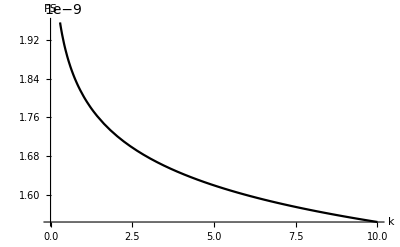

```mathematica
Plot[PSsr2[teval[k]],{k,0.0001,10},PlotStyle->{Red,Black},AxesLabel->{k,PS}]
```

```mathematica
(*Para el paper*)
PSsr=PSsr2[teval[0.05]]
LogPSsr=Log[10^(10) PSsr2[teval[0.05]]]
nSsr=nSsr2[teval[0.05]]
rsr=rsr[teval[0.002]]
```

2.18548×10^-9+0. ⅈ

3.08442+0. ⅈ

0.93801+0. ⅈ

1.89904×10^-6+0. ⅈ

```mathematica
PSnum:=2.2023 10^(-9)
LogPSnum:=3.092
nSnum:=0.9632
rnum:=0.00335
```

```mathematica
EPS=(Abs[PSsr-PSnum]/PSnum )100
ELogPS=(Abs[LogPSsr-LogPSnum]/LogPSnum )100
EnS=(Abs[nSsr-nSnum]/nSnum )100
Er=(Abs[rsr-rnum]/rnum )100
```

0.763708

0.245118

2.61523

99.9433

```mathematica
k:=0.05
PSsr1[teval[k]]
nSsr1[teval[k]]
```

2.18095×10^-9+0. ⅈ

0.937042+0. ⅈ

```mathematica
k:=0.05
PTsr1[teval[k]]
nTsr1[teval[k]]
```

6.02213×10^-16+0. ⅈ

-2.88809×10^-7+0. ⅈ

```mathematica
k:=0.001
PSsr2[teval[k]]
nSsr2[teval[k]]
```

2.7591×10^-9+0. ⅈ

0.942652+0. ⅈ

```mathematica
k:=0.05
PTsr2[teval[k]]
nTsr2[teval[k]]
```

6.02213×10^-16+0. ⅈ

-2.93725×10^-7+0. ⅈ

```mathematica
Plot[PSsr2[teval[k]],{k,0.0001,10},PlotStyle->{Red,Black},AxesLabel->{k,PS}]
```

-Graphics-

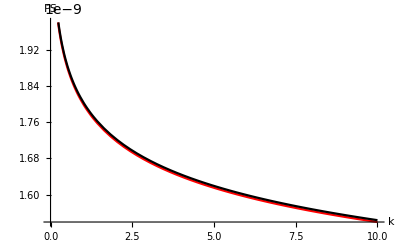

```mathematica
Plot[{PSsr1[teval[k]],PSsr2[teval[k]]},{k,0.0001,10},PlotStyle->{Red,Black},AxesLabel->{k,PS}]
```

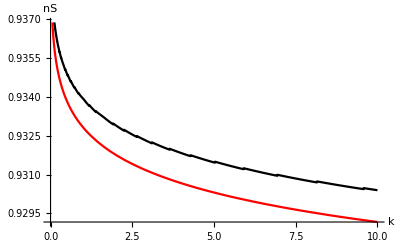

```mathematica
Plot[{nSsr1[teval[k]],nSsr2[teval[k]]},{k,0,10},PlotStyle->{Red,Black},AxesLabel->{k,nS}]
```

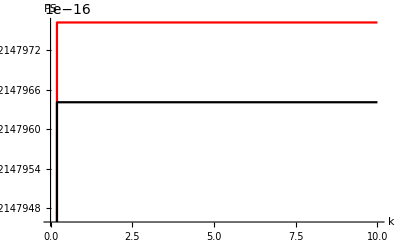

```mathematica
Plot[{PTsr1[teval[kcomoving[k]]],PTsr2[teval[kcomoving[k]]]},{k,0.0001,10},PlotStyle->{Red,Black},AxesLabel->{k,PS}]
```

```mathematica
(*Clear[k];
strm=OpenWrite["//Users/crojas/Documents/Research/inflation/exponential/graphs/PS_sr.dat",FormatType->OutputForm];
For[i=0,i<100000,Write[strm,k=N[i/10000],"   ",CForm[PSsr[teval[k]]]],i++]
Close[strm];
Clear[k];
strm=OpenWrite["//Users/crojas/Documents/Research/inflation/exponential/graphs/nS_sr.dat",FormatType->OutputForm];
For[i=0,i<100000,Write[strm,k=N[i/10000],"   ",CForm[nSsr[teval[k]]]],i++]
Close[strm];*)
```

```mathematica
(*Log*)
```

```mathematica
premarcas1=Table[10^i,{i,1/5,1,1/5}];
marcas1={.0001};
Do[AppendTo[marcas1,Table[N[premarcas1[[i]]/10^(5-j)],{i,1,Length[premarcas1]}]],{j,1,5}];
marcas1=Flatten[marcas1]
```

{0.0001,0.000158489,0.000251189,0.000398107,0.000630957,0.001,0.00158489,0.00251189,0.00398107,0.00630957,0.01,0.0158489,0.0251189,0.0398107,0.0630957,0.1,0.158489,0.251189,0.398107,0.630957,1.,1.58489,2.51189,3.98107,6.30957,10.}

```mathematica
powerspectra=Table[k=marcas1[[i]];{k,PSsr[teval[k]]},{i,1,Length[marcas1]}]
```

InterpolatingFunction::dmval: Input value {3.5473×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.40004×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.0001,(2.12486×10^-9+0. ⅈ)[62059.4]},{0.000158489,(2.12486×10^-9+0. ⅈ)[81830.8]},{0.000251189,(2.12486×10^-9+0. ⅈ)[101629.]},{0.000398107,(2.12486×10^-9+0. ⅈ)[121454.]},{0.000630957,(2.12486×10^-9+0. ⅈ)[141306.]},{0.001,(2.12486×10^-9+0. ⅈ)[161185.]},{0.00158489,(2.12486×10^-9+0. ⅈ)[181092.]},{0.00251189,(2.12486×10^-9+0. ⅈ)[201027.]},{0.00398107,(2.12486×10^-9+0. ⅈ)[220990.]},{0.00630957,(2.12486×10^-9+0. ⅈ)[240981.]},{0.01,(2.12486×10^-9+0. ⅈ)[261002.]},{0.0158489,(2.12486×10^-9+0. ⅈ)[281051.]},{0.0251189,(2.12486×10^-9+0. ⅈ)[301130.]},{0.0398107,(2.12486×10^-9+0. ⅈ)[321238.]},{0.0630957,(2.12486×10^-9+0. ⅈ)[341376.]},{0.1,(2.12486×10^-9+0. ⅈ)[361545.]},{0.158489,(2.12486×10^-9+0. ⅈ)[381744.]},{0.251189,(2.12486×10^-9+0. ⅈ)[401974.]},{0.398107,(2.12486×10^-9+0. ⅈ)[422235.]},{0.630957,(2.12486×10^-9+0. ⅈ)[442528.]},{1.,(2.12486×10^-9+0. ⅈ)[462853.]},{1.58489,(2.12486×10^-9+0. ⅈ)[483210.]},{2.51189,(2.12486×10^-9+0. ⅈ)[503600.]},{3.98107,(2.12486×10^-9+0. ⅈ)[524023.]},{6.30957,(2.12486×10^-9+0. ⅈ)[544479.]},{10.,(2.12486×10^-9+0. ⅈ)[564969.]}}

```mathematica
fit=NonlinearModelFit[powerspectra,cons x^(spec-1),{spec,cons},x]
```

NonlinearModelFit::nrlnum: The function value {1.-1. (2.12486×10^-9+0. ⅈ)[62059.4],1.-1. (2.12486×10^-9+0. ⅈ)[81830.8],1.-1. (2.12486×10^-9+0. ⅈ)[101629.],1.-1. (2.12486×10^-9+0. ⅈ)[121454.],1.-1. «1»,«1»,«1»,1.-«1»,1.-1. (2.12486×10^-9+0. ⅈ)[220990.],1.-1. (2.12486×10^-9+0. ⅈ)[240981.],«16»} is not a list of real numbers with dimensions {26} at {spec,cons} = {1.,1.}.

NonlinearModelFit[{{0.0001,(2.12486×10^-9+0. ⅈ)[62059.4]},{0.000158489,(2.12486×10^-9+0. ⅈ)[81830.8]},{0.000251189,(2.12486×10^-9+0. ⅈ)[101629.]},{0.000398107,(2.12486×10^-9+0. ⅈ)[121454.]},{0.000630957,(2.12486×10^-9+0. ⅈ)[141306.]},{0.001,(2.12486×10^-9+0. ⅈ)[161185.]},{0.00158489,(2.12486×10^-9+0. ⅈ)[181092.]},{0.00251189,(2.12486×10^-9+0. ⅈ)[201027.]},{0.00398107,(2.12486×10^-9+0. ⅈ)[220990.]},{0.00630957,(2.12486×10^-9+0. ⅈ)[240981.]},{0.01,(2.12486×10^-9+0. ⅈ)[261002.]},{0.0158489,(2.12486×10^-9+0. ⅈ)[281051.]},{0.0251189,(2.12486×10^-9+0. ⅈ)[301130.]},{0.0398107,(2.12486×10^-9+0. ⅈ)[321238.]},{0.0630957,(2.12486×10^-9+0. ⅈ)[341376.]},{0.1,(2.12486×10^-9+0. ⅈ)[361545.]},{0.158489,(2.12486×10^-9+0. ⅈ)[381744.]},{0.251189,(2.12486×10^-9+0. ⅈ)[401974.]},{0.398107,(2.12486×10^-9+0. ⅈ)[422235.]},{0.630957,(2.12486×10^-9+0. ⅈ)[442528.]},{1.,(2.12486×10^-9+0. ⅈ)[462853.]},{1.58489,(2.12486×10^-9+0. ⅈ)[483210.]},{2.51189,(2.12486×10^-9+0. ⅈ)[503600.]},{3.98107,(2.12486×10^-9+0. ⅈ)[524023.]},{6.30957,(2.12486×10^-9+0. ⅈ)[544479.]},{10.,(2.12486×10^-9+0. ⅈ)[564969.]}},cons x^(-1+spec),{spec,cons},x]

```mathematica
fit["BestFitParameters"]
```

NonlinearModelFit::nrlnum: The function value {1.-1. (2.12486×10^-9+0. ⅈ)[62059.4],1.-1. (2.12486×10^-9+0. ⅈ)[81830.8],1.-1. (2.12486×10^-9+0. ⅈ)[101629.],1.-1. (2.12486×10^-9+0. ⅈ)[121454.],1.-1. «1»,«1»,«1»,1.-«1»,1.-1. (2.12486×10^-9+0. ⅈ)[220990.],1.-1. (2.12486×10^-9+0. ⅈ)[240981.],«16»} is not a list of real numbers with dimensions {26} at {spec,cons} = {1.,1.}.

NonlinearModelFit[{{0.0001,(2.12486×10^-9+0. ⅈ)[62059.4]},{0.000158489,(2.12486×10^-9+0. ⅈ)[81830.8]},{0.000251189,(2.12486×10^-9+0. ⅈ)[101629.]},{0.000398107,(2.12486×10^-9+0. ⅈ)[121454.]},{0.000630957,(2.12486×10^-9+0. ⅈ)[141306.]},{0.001,(2.12486×10^-9+0. ⅈ)[161185.]},{0.00158489,(2.12486×10^-9+0. ⅈ)[181092.]},{0.00251189,(2.12486×10^-9+0. ⅈ)[201027.]},{0.00398107,(2.12486×10^-9+0. ⅈ)[220990.]},{0.00630957,(2.12486×10^-9+0. ⅈ)[240981.]},{0.01,(2.12486×10^-9+0. ⅈ)[261002.]},{0.0158489,(2.12486×10^-9+0. ⅈ)[281051.]},{0.0251189,(2.12486×10^-9+0. ⅈ)[301130.]},{0.0398107,(2.12486×10^-9+0. ⅈ)[321238.]},{0.0630957,(2.12486×10^-9+0. ⅈ)[341376.]},{0.1,(2.12486×10^-9+0. ⅈ)[361545.]},{0.158489,(2.12486×10^-9+0. ⅈ)[381744.]},{0.251189,(2.12486×10^-9+0. ⅈ)[401974.]},{0.398107,(2.12486×10^-9+0. ⅈ)[422235.]},{0.630957,(2.12486×10^-9+0. ⅈ)[442528.]},{1.,(2.12486×10^-9+0. ⅈ)[462853.]},{1.58489,(2.12486×10^-9+0. ⅈ)[483210.]},{2.51189,(2.12486×10^-9+0. ⅈ)[503600.]},{3.98107,(2.12486×10^-9+0. ⅈ)[524023.]},{6.30957,(2.12486×10^-9+0. ⅈ)[544479.]},{10.,(2.12486×10^-9+0. ⅈ)[564969.]}},cons x^(-1+spec),{spec,cons},x][BestFitParameters]

```mathematica
strm=OpenWrite["/Users/crojas/Documents/Research/inflation/gStarobinsky/slow-roll/graph/PSsr2_p=1.0004.dat",FormatType->OutputForm];
For[i=0,i<Length[marcas1],Write[strm,k=marcas1[[i]],"   ",CForm[PSsr2[teval[k]]]],i++]
Close[strm];
```

OpenWrite::noopen: Cannot open /Users/crojas/Documents/Research/inflation/gStarobinsky/slow-roll/graph/PSsr2_p=1.0004.dat.

Write::strml: $Failed is not a string, stream, or list of strings and streams.

General::stop: Further output of Write::strml will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.5473×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.40004×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

```mathematica
strm=OpenWrite["/Users/crojas/Documents/Research/inflation/gStarobinsky/slow-roll/graph/PTsr2_p=1.0004_kcomoving.dat",FormatType->OutputForm];
For[i=0,i<Length[marcas1],Write[strm,k=marcas1[[i]],"   ",CForm[PTsr2[teval[kcomoving[k]]]]],i++]
Close[strm];
```

InterpolatingFunction::dmval: Input value {1.21001×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Parameters*)
(*H1[t_]:=(4 (1+ⅇ^(√(2/3) ϕsr[t]) (-1+p)-2 p)^2)/(3 (-1+ⅇ^(√(2/3) ϕsr[t]))^2 (1-2 p)^2)
δH1[t_]:=(8 (1-2 p)^2+8 ⅇ^(2 √(2/3) ϕsr[t]) (-1+p)^2-4 ⅇ^(√(2/3) ϕsr[t]) (-1+2 p) (-4+5 p))/(3 (-1+ⅇ^(√(2/3) ϕsr[t]))^2 (1-2 p)^2)*)
```

```mathematica
(*asr and ϕsr*)
```

```mathematica
strm=OpenWrite["/Users/crojas/Documents/Research/inflation/gStarobinsky/slow-roll/graph/asr_p=1.0004.dat",FormatType->OutputForm];
For[i=0,i<100000,Write[strm,CForm[100 i],"    ",CForm[Re[asr[100 i]]]],i++]
Close[strm];
```

```mathematica
strm=OpenWrite["/Users/crojas/Documents/Research/inflation/gStarobinsky/slow-roll/graph/phisr_p=1.0004.dat",FormatType->OutputForm];
For[i=0,i<100000,Write[strm,CForm[100 i],"    ",CForm[Re[ϕsr[100 i]]]],i++]
Close[strm];
```

InterpolatingFunction::dmval: Input value {9800100} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9800200} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9800300} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.